```mathematica
<<RLBot`;
```

```mathematica
data = ImportNDJSON["drive_up_quarterpipe.ndjson", {2}];
```

```mathematica
x = #["car"]["x"] & /@ data;
v = #["car"]["v"] & /@ data;
f = #["car"]["o"][[All, 1]] & /@ data;
wLocal = (#["car"]["w"].#["car"]["o"]) & /@ data;
o = #["car"]["o"] & /@ data;
```

```mathematica
Graphics3D[Line[x]]
```

-Graphics3D-

```mathematica
GraphicsRow[{MatrixForm[x], MatrixForm[wLocal]}]
```

```mathematica
wLocal
```

{{0.000426439,-0.000393641,0.00231419},{0.000380382,-0.000393684,0.00711397},{0.000341037,-0.000393727,0.0112138},{0.000308402,-0.00039377,0.0146136},{0.000280562,-0.000393813,0.0175135},{0.000256518,-0.000393899,0.0200134},262,{-0.0231005,0.0236865,0.00969242},{-0.0198995,0.0206846,0.00971507},{-0.0171278,0.018071,0.00974688},{-0.0147878,0.0158509,0.00977068},{-0.0127265,0.0138627,0.00978722},{-0.011039,0.0120732,0.00980367}}
 |  |  |  |

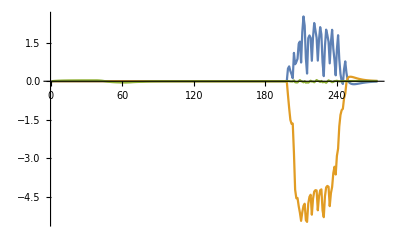

```mathematica
ListLinePlot[Transpose[wLocal], PlotRange->All]
```

```mathematica
wLocalAvg = MovingAverage[wLocal, 10];
```

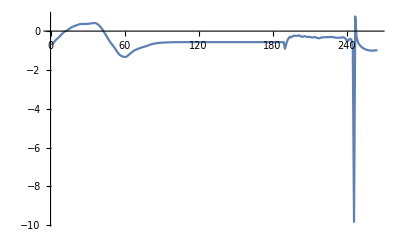

```mathematica
ListLinePlot[wLocalAvg[[All, 1]]/wLocalAvg[[All, 2]], PlotRange->All]
```

```mathematica
ArrayFlatten[{{x, v, wLocal}}] // MatrixForm
```

(1708.82 | 1379.33 | 17.01 | 1257.39 | -393.441 | 0.211 | 0.000426439 | -0.000393641 | 0.00231419
1719.3 | 1376.05 | 17.01 | 1257.41 | -393.511 | 0.211 | 0.000380382 | -0.000393684 | 0.00711397
1729.78 | 1372.77 | 17.01 | 1257.44 | -393.561 | 0.211 | 0.000341037 | -0.000393727 | 0.0112138
1740.26 | 1369.49 | 17.01 | 1257.48 | -393.581 | 0.211 | 0.000308402 | -0.00039377 | 0.0146136
1750.74 | 1366.21 | 17.01 | 1257.53 | -393.581 | 0.211 | 0.000280562 | -0.000393813 | 0.0175135
1761.22 | 1362.93 | 17.01 | 1257.59 | -393.551 | 0.211 | 0.000256518 | -0.000393899 | 0.0200134
1771.7 | 1359.65 | 17.01 | 1257.65 | -393.491 | 0.211 | 0.000236309 | -0.000393985 | 0.0221133
1782.18 | 1356.37 | 17.01 | 1257.72 | -393.401 | 0.211 | 0.000218977 | -0.00039407 | 0.0239132
1792.66 | 1353.09 | 17.01 | 1257.8 | -393.291 | 0.211 | 0.00020452 | -0.000394156 | 0.0254131
1803.14 | 1349.81 | 17.01 | 1257.89 | -393.161 | 0.211 | 0.000191944 | -0.000394285 | 0.0267131
1813.62 | 1346.53 | 17.01 | 1257.98 | -393.011 | 0.211 | 0.0000858749 | -0.000424188 | 0.0278121
1824.1 | 1343.26 | 17.01 | 1258.08 | -392.831 | 0.211 | 0.0000771651 | -0.000424255 | 0.0287121
1834.58 | 1339.99 | 17.01 | 1258.19 | -392.641 | 0.211 | 0.0000693733 | -0.000424357 | 0.029512
1845.07 | 1336.72 | 17.01 | 1258.3 | -392.431 | 0.211 | 0.0000625401 | -0.000424458 | 0.030212
1855.56 | 1333.45 | 17.01 | 1258.42 | -392.201 | 0.211 | 0.0000567064 | -0.000424525 | 0.030812
1866.05 | 1330.18 | 17.01 | 1258.54 | -391.961 | 0.211 | 0.0000517907 | -0.000424627 | 0.0313119
1876.54 | 1326.92 | 17.01 | 1258.66 | -391.701 | 0.211 | -0.0000486177 | -0.000454398 | 0.031811
1887.03 | 1323.66 | 17.01 | 1258.79 | -391.431 | 0.211 | -0.0000525833 | -0.000454472 | 0.032211
1897.52 | 1320.4 | 17.01 | 1258.92 | -391.151 | 0.211 | -0.0000555902 | -0.000454545 | 0.032511
1908.01 | 1317.14 | 17.01 | 1259.05 | -390.861 | 0.211 | -0.0000585971 | -0.000454619 | 0.0328109
1918.5 | 1313.89 | 17.01 | 1259.19 | -390.571 | 0.211 | -0.0000616041 | -0.000454693 | 0.0331109
1928.99 | 1310.64 | 17.01 | 1259.33 | -390.271 | 0.211 | -0.0000636523 | -0.000454766 | 0.0333109
1939.49 | 1307.39 | 17.01 | 1259.47 | -389.971 | 0.211 | -0.0000657006 | -0.00045484 | 0.0335109
1949.99 | 1304.14 | 17.01 | 1259.61 | -389.661 | 0.211 | -0.000172856 | -0.000487339 | 0.0337099
1960.49 | 1300.9 | 17.01 | 1259.75 | -389.341 | 0.211 | -0.000173955 | -0.000487382 | 0.0338099
1970.99 | 1297.66 | 17.01 | 1259.89 | -389.021 | 0.211 | -0.000175054 | -0.000487425 | 0.0339099
1981.49 | 1294.42 | 17.01 | 1260.04 | -388.691 | 0.211 | -0.000176106 | -0.000487454 | 0.0340099
1991.99 | 1291.18 | 17.01 | 1260.19 | -388.361 | 0.211 | -0.000177205 | -0.000487497 | 0.0341099
2002.49 | 1287.95 | 17.01 | 1260.34 | -388.031 | 0.211 | -0.000178304 | -0.00048754 | 0.0342099
2012.99 | 1284.72 | 17.01 | 1260.49 | -387.701 | 0.211 | -0.000179403 | -0.000487583 | 0.0343099
2023.5 | 1281.49 | 17.01 | 1260.64 | -387.361 | 0.211 | -0.000180502 | -0.000487626 | 0.0344098
2034.01 | 1278.26 | 17.01 | 1260.79 | -387.021 | 0.211 | -0.000180642 | -0.000487669 | 0.0344098
2044.52 | 1275.04 | 17.01 | 1260.94 | -386.681 | 0.211 | -0.000180783 | -0.000487712 | 0.0344098
2055.03 | 1271.82 | 17.01 | 1261.09 | -386.341 | 0.211 | -0.000180923 | -0.000487755 | 0.0344098
2065.54 | 1268.6 | 17.01 | 1261.24 | -386.001 | 0.211 | -0.000181063 | -0.000487798 | 0.0344098
2076.05 | 1265.39 | 17.01 | 1261.39 | -385.661 | 0.211 | -0.000181203 | -0.00048784 | 0.0344098
2086.56 | 1262.18 | 17.01 | 1261.54 | -385.321 | 0.211 | -0.000181297 | -0.000487869 | 0.0344098
2097.07 | 1258.97 | 17.01 | 1261.69 | -384.981 | 0.211 | -0.000181437 | -0.000487912 | 0.0344098
2107.59 | 1255.76 | 17.01 | 1261.84 | -384.641 | 0.211 | -0.000182536 | -0.000487954 | 0.0345098
2118.11 | 1252.56 | 17.01 | 1261.96 | -384.391 | 0.211 | -0.000185846 | -0.000392311 | 0.0318097
2128.63 | 1249.36 | 17.01 | 1262.08 | -384.131 | 0.211 | -0.000163908 | -0.000392346 | 0.0295098
2139.15 | 1246.16 | 17.01 | 1262.18 | -383.951 | 0.211 | -0.000224188 | -0.000424279 | 0.024809
2149.67 | 1242.96 | 17.01 | 1262.28 | -383.761 | 0.211 | -0.000186879 | -0.000424282 | 0.0209092
2160.19 | 1239.76 | 17.01 | 1262.35 | -383.661 | 0.211 | -0.0002251 | -0.000453266 | 0.0149085
2170.71 | 1236.56 | 17.01 | 1262.4 | -383.651 | 0.211 | -0.000151322 | -0.000453258 | 0.00720888
2181.23 | 1233.36 | 17.01 | 1262.45 | -383.621 | 0.211 | -0.0000890047 | -0.000453258 | 0.000709179
2191.75 | 1230.16 | 17.01 | 1262.47 | -383.691 | 0.211 | -0.0000120716 | -0.000453266 | -0.00731045
2202.27 | 1226.96 | 17.01 | 1262.49 | -383.761 | 0.211 | 0.000053165 | -0.000453274 | -0.0141101
2212.79 | 1223.76 | 17.01 | 1262.51 | -383.851 | 0.211 | 0.000107899 | -0.00045329 | -0.0198099
2223.31 | 1220.56 | 17.01 | 1262.52 | -383.961 | 0.211 | 0.000154005 | -0.000453305 | -0.0246097
2233.83 | 1217.36 | 17.01 | 1262.52 | -384.091 | 0.211 | 0.000192484 | -0.000453329 | -0.0286095
2244.35 | 1214.16 | 17.01 | 1262.51 | -384.251 | 0.211 | 0.000225168 | -0.000453345 | -0.0320093
2254.87 | 1210.96 | 17.01 | 1262.5 | -384.441 | 0.211 | 0.000253101 | -0.000453368 | -0.0349092
2265.39 | 1207.75 | 17.01 | 1262.48 | -384.671 | 0.211 | 0.000276284 | -0.000453399 | -0.0373091
2275.91 | 1204.54 | 17.01 | 1262.45 | -384.931 | 0.211 | 0.000296548 | -0.000453423 | -0.039409
2286.43 | 1201.33 | 17.01 | 1262.41 | -385.211 | 0.211 | 0.000408657 | -0.000424251 | -0.041108
2296.95 | 1198.12 | 17.01 | 1262.36 | -385.521 | 0.211 | 0.000423159 | -0.000424247 | -0.0426079
2307.47 | 1194.9 | 17.01 | 1262.3 | -385.861 | 0.211 | 0.000435786 | -0.000424241 | -0.0439078
2317.99 | 1191.68 | 17.01 | 1262.23 | -386.221 | 0.211 | 0.000446494 | -0.000424236 | -0.0450078
2328.51 | 1188.46 | 17.01 | 1262.16 | -386.601 | 0.211 | 0.000455285 | -0.00042423 | -0.0459077
2339.03 | 1185.24 | 17.01 | 1262.08 | -387.001 | 0.211 | 0.000568259 | -0.000391909 | -0.0467067
2349.55 | 1182.01 | 17.01 | 1262. | -387.421 | 0.211 | 0.000575121 | -0.000391863 | -0.0474067
2360.07 | 1178.78 | 17.01 | 1261.91 | -387.851 | 0.211 | 0.000580986 | -0.000391828 | -0.0480066
2370.59 | 1175.54 | 17.01 | 1261.84 | -388.201 | 0.211 | 0.000560044 | -0.000391782 | -0.0458067
2381.1 | 1172.3 | 17.01 | 1261.77 | -388.581 | 0.211 | 0.000542937 | -0.000391736 | -0.0440068
2391.61 | 1169.06 | 17.01 | 1261.69 | -388.981 | 0.211 | 0.000528707 | -0.000391689 | -0.0425069
2402.12 | 1165.81 | 17.01 | 1261.61 | -389.391 | 0.211 | 0.000516394 | -0.000391643 | -0.0412069
2412.63 | 1162.56 | 17.01 | 1261.56 | -389.711 | 0.211 | 0.000480112 | -0.000391596 | -0.0374071
2423.14 | 1159.31 | 17.01 | 1261.5 | -390.051 | 0.211 | 0.000449546 | -0.000391561 | -0.0342073
2433.65 | 1156.06 | 17.01 | 1261.44 | -390.391 | 0.211 | 0.000424731 | -0.000391526 | -0.0316074
2444.16 | 1152.8 | 17.01 | 1261.38 | -390.741 | 0.211 | 0.000403715 | -0.000391503 | -0.0294075
2454.67 | 1149.54 | 17.01 | 1261.32 | -391.081 | 0.211 | 0.000386533 | -0.00039148 | -0.0276076
2465.18 | 1146.28 | 17.01 | 1261.26 | -391.411 | 0.211 | 0.000371306 | -0.000391445 | -0.0260076
2475.69 | 1143.02 | 17.01 | 1261.2 | -391.741 | 0.211 | 0.000358917 | -0.000391421 | -0.0247077
2486.2 | 1139.75 | 17.01 | 1261.15 | -392.061 | 0.211 | 0.000348446 | -0.000391398 | -0.0236077
2507.22 | 1133.21 | 17.01 | 1261.05 | -392.671 | 0.211 | 0.000332298 | -0.000391351 | -0.0219078
2517.73 | 1129.94 | 17.01 | 1261. | -392.961 | 0.211 | 0.000325662 | -0.000391327 | -0.0212079
2528.24 | 1126.66 | 17.01 | 1260.99 | -393.151 | 0.211 | 0.000428887 | -0.00045393 | -0.0179067
2538.75 | 1123.38 | 17.01 | 1260.98 | -393.341 | 0.211 | 0.00040213 | -0.000453881 | -0.0151068
2549.26 | 1120.1 | 17.01 | 1260.97 | -393.531 | 0.211 | 0.000380122 | -0.000453856 | -0.0128069
2559.77 | 1116.82 | 17.01 | 1260.96 | -393.711 | 0.211 | 0.00036195 | -0.000453832 | -0.010907
2570.28 | 1113.54 | 17.01 | 1260.95 | -393.881 | 0.211 | 0.000346611 | -0.000453832 | -0.0093071
2580.79 | 1110.26 | 17.01 | 1260.94 | -394.041 | 0.211 | 0.000333232 | -0.000453807 | -0.00790717
2591.3 | 1106.98 | 17.01 | 1260.94 | -394.191 | 0.211 | 0.000321771 | -0.000453782 | -0.00670722
2601.81 | 1103.69 | 17.01 | 1260.94 | -394.331 | 0.211 | 0.000312184 | -0.000453782 | -0.00570727
2612.32 | 1100.4 | 17.01 | 1260.94 | -394.461 | 0.211 | 0.000304557 | -0.000453758 | -0.00490731
2622.83 | 1097.11 | 17.01 | 1260.95 | -394.581 | 0.211 | 0.000297846 | -0.000453758 | -0.00420734
2633.34 | 1093.82 | 17.01 | 1260.96 | -394.691 | 0.211 | 0.000292094 | -0.000453758 | -0.00360737
2643.85 | 1090.53 | 17.01 | 1260.97 | -394.791 | 0.211 | 0.000287344 | -0.000453733 | -0.00310739
2654.36 | 1087.24 | 17.01 | 1260.99 | -394.881 | 0.211 | 0.00028255 | -0.000453733 | -0.00260741
2664.87 | 1083.95 | 17.01 | 1261.01 | -394.961 | 0.211 | 0.000278715 | -0.000453733 | -0.00220743
2675.38 | 1080.66 | 17.01 | 1261.03 | -395.031 | 0.211 | 0.000275839 | -0.000453733 | -0.00190744
2685.89 | 1077.37 | 17.01 | 1261.05 | -395.101 | 0.211 | 0.000272963 | -0.000453733 | -0.00160746
2696.4 | 1074.08 | 17.01 | 1261.08 | -395.161 | 0.211 | 0.000271045 | -0.000453733 | -0.00140747
2706.91 | 1070.79 | 17.01 | 1261.11 | -395.211 | 0.211 | 0.000269128 | -0.000453733 | -0.00120748
2717.42 | 1067.5 | 17.01 | 1261.14 | -395.261 | 0.211 | 0.000267254 | -0.000453708 | -0.00100748
2727.93 | 1064.21 | 17.01 | 1261.17 | -395.311 | 0.211 | 0.000265337 | -0.000453708 | -0.000807493
2738.44 | 1060.92 | 17.01 | 1261.2 | -395.351 | 0.211 | 0.000264378 | -0.000453708 | -0.000707498
2748.95 | 1057.62 | 17.01 | 1261.23 | -395.391 | 0.211 | 0.000263419 | -0.000453708 | -0.000607502
2759.46 | 1054.32 | 17.01 | 1261.26 | -395.421 | 0.211 | 0.00026246 | -0.000453708 | -0.000507507
2769.97 | 1051.02 | 17.01 | 1261.29 | -395.451 | 0.211 | 0.000261502 | -0.000453708 | -0.000407512
2780.48 | 1047.72 | 17.01 | 1261.33 | -395.481 | 0.211 | 0.000260543 | -0.000453708 | -0.000307516
2790.99 | 1044.42 | 17.01 | 1261.37 | -395.511 | 0.211 | 0.000259584 | -0.000453708 | -0.000207521
2801.5 | 1041.12 | 17.01 | 1261.41 | -395.531 | 0.211 | 0.000258626 | -0.000453708 | -0.000107525
2812.01 | 1037.82 | 17.01 | 1261.45 | -395.551 | 0.211 | 0.000258626 | -0.000453708 | -0.000107525
2822.52 | 1034.52 | 17.01 | 1261.49 | -395.571 | 0.211 | 0.000258626 | -0.000453708 | -0.000107525
2833.03 | 1031.22 | 17.01 | 1261.53 | -395.591 | 0.211 | 0.000258626 | -0.000453708 | -0.000107525
2843.54 | 1027.92 | 17.01 | 1261.57 | -395.611 | 0.211 | 0.000258626 | -0.000453708 | -0.000107525
2854.05 | 1024.62 | 17.01 | 1261.61 | -395.631 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
2864.56 | 1021.32 | 17.01 | 1261.65 | -395.651 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
2875.07 | 1018.02 | 17.01 | 1261.69 | -395.661 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
2885.58 | 1014.72 | 17.01 | 1261.73 | -395.681 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
2896.09 | 1011.42 | 17.01 | 1261.77 | -395.691 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
2906.61 | 1008.12 | 17.01 | 1261.81 | -395.701 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
2917.13 | 1004.82 | 17.01 | 1261.85 | -395.711 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
2927.65 | 1001.52 | 17.01 | 1261.89 | -395.731 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
2938.17 | 998.22 | 17.01 | 1261.93 | -395.741 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
2948.69 | 994.92 | 17.01 | 1261.97 | -395.751 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
2959.21 | 991.62 | 17.01 | 1262.01 | -395.761 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
2969.73 | 988.32 | 17.01 | 1262.05 | -395.781 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
2980.25 | 985.02 | 17.01 | 1262.09 | -395.791 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
2990.77 | 981.72 | 17.01 | 1262.13 | -395.801 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3001.29 | 978.42 | 17.01 | 1262.17 | -395.811 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3011.81 | 975.12 | 17.01 | 1262.21 | -395.831 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3022.33 | 971.82 | 17.01 | 1262.25 | -395.841 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3032.85 | 968.52 | 17.01 | 1262.29 | -395.851 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3043.37 | 965.22 | 17.01 | 1262.33 | -395.861 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3053.89 | 961.92 | 17.01 | 1262.37 | -395.881 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3064.41 | 958.62 | 17.01 | 1262.41 | -395.891 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3074.93 | 955.32 | 17.01 | 1262.45 | -395.901 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3085.45 | 952.02 | 17.01 | 1262.49 | -395.911 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3095.97 | 948.72 | 17.01 | 1262.53 | -395.931 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3106.49 | 945.42 | 17.01 | 1262.57 | -395.941 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3117.01 | 942.12 | 17.01 | 1262.61 | -395.951 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3127.53 | 938.82 | 17.01 | 1262.65 | -395.961 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3138.05 | 935.52 | 17.01 | 1262.69 | -395.981 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3148.57 | 932.22 | 17.01 | 1262.73 | -395.991 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3159.09 | 928.92 | 17.01 | 1262.77 | -396.001 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3169.61 | 925.62 | 17.01 | 1262.81 | -396.011 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3180.13 | 922.32 | 17.01 | 1262.85 | -396.031 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3190.65 | 919.02 | 17.01 | 1262.89 | -396.041 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3201.17 | 915.72 | 17.01 | 1262.93 | -396.051 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3211.69 | 912.42 | 17.01 | 1262.97 | -396.061 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3222.22 | 909.12 | 17.01 | 1263.01 | -396.081 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3232.75 | 905.82 | 17.01 | 1263.05 | -396.091 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3243.28 | 902.52 | 17.01 | 1263.09 | -396.101 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3253.81 | 899.22 | 17.01 | 1263.13 | -396.111 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3264.34 | 895.92 | 17.01 | 1263.17 | -396.131 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3274.87 | 892.62 | 17.01 | 1263.21 | -396.141 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3285.4 | 889.32 | 17.01 | 1263.25 | -396.151 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3295.93 | 886.02 | 17.01 | 1263.29 | -396.161 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3306.46 | 882.72 | 17.01 | 1263.33 | -396.181 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3316.99 | 879.42 | 17.01 | 1263.37 | -396.191 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3327.52 | 876.12 | 17.01 | 1263.41 | -396.201 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3338.05 | 872.82 | 17.01 | 1263.45 | -396.211 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3348.58 | 869.52 | 17.01 | 1263.49 | -396.231 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3359.11 | 866.22 | 17.01 | 1263.53 | -396.241 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3369.64 | 862.92 | 17.01 | 1263.57 | -396.251 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3380.17 | 859.62 | 17.01 | 1263.61 | -396.261 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3390.7 | 856.32 | 17.01 | 1263.65 | -396.281 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3401.23 | 853.02 | 17.01 | 1263.69 | -396.291 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3411.76 | 849.72 | 17.01 | 1263.73 | -396.301 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3422.29 | 846.42 | 17.01 | 1263.77 | -396.311 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3432.82 | 843.12 | 17.01 | 1263.81 | -396.331 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3443.35 | 839.82 | 17.01 | 1263.85 | -396.341 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3453.88 | 836.52 | 17.01 | 1263.89 | -396.351 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3464.41 | 833.22 | 17.01 | 1263.93 | -396.361 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3474.94 | 829.92 | 17.01 | 1263.97 | -396.381 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3485.47 | 826.62 | 17.01 | 1264.01 | -396.391 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3496. | 823.32 | 17.01 | 1264.05 | -396.401 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3506.53 | 820.02 | 17.01 | 1264.09 | -396.411 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3517.06 | 816.72 | 17.01 | 1264.13 | -396.431 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3527.59 | 813.42 | 17.01 | 1264.17 | -396.441 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3538.12 | 810.12 | 17.01 | 1264.21 | -396.451 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3548.66 | 806.82 | 17.01 | 1264.25 | -396.461 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3559.2 | 803.52 | 17.01 | 1264.29 | -396.481 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3569.74 | 800.22 | 17.01 | 1264.33 | -396.491 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3580.28 | 796.92 | 17.01 | 1264.37 | -396.501 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3590.82 | 793.62 | 17.01 | 1264.41 | -396.511 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3601.36 | 790.32 | 17.01 | 1264.45 | -396.531 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3611.9 | 787.02 | 17.01 | 1264.49 | -396.541 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3622.44 | 783.72 | 17.01 | 1264.53 | -396.551 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3632.98 | 780.42 | 17.01 | 1264.57 | -396.561 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3643.52 | 777.12 | 17.01 | 1264.61 | -396.581 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3654.06 | 773.81 | 17.01 | 1264.65 | -396.591 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3664.6 | 770.5 | 17.01 | 1264.69 | -396.601 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3675.14 | 767.19 | 17.01 | 1264.73 | -396.621 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3685.68 | 763.88 | 17.01 | 1264.77 | -396.631 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3696.22 | 760.57 | 17.01 | 1264.81 | -396.641 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3706.76 | 757.26 | 17.01 | 1264.85 | -396.651 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3717.3 | 753.95 | 17.01 | 1264.89 | -396.671 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3727.84 | 750.64 | 17.01 | 1264.93 | -396.681 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3738.38 | 747.33 | 17.01 | 1264.97 | -396.691 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3748.92 | 744.02 | 17.01 | 1265.01 | -396.701 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3759.46 | 740.71 | 17.01 | 1265.05 | -396.721 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3770. | 737.4 | 17.01 | 1265.09 | -396.731 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3780.54 | 734.09 | 17.01 | 1265.13 | -396.741 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3791.08 | 730.78 | 17.01 | 1265.17 | -396.751 | 0.211 | 0.000257571 | -0.000453708 | 2.46951×10^-6
3801.61 | 727.46 | 17.13 | 1263.16 | -398.051 | 14.911 | 0.496435 | -0.544179 | 0.00827609
3812.12 | 724.13 | 17.37 | 1261.16 | -399.271 | 28.891 | 0.581514 | -1.05284 | 0.00295882
3822.62 | 720.8 | 17.72 | 1259.58 | -399.751 | 42.211 | 0.400202 | -1.50627 | -0.00671363
3833.11 | 717.47 | 18.12 | 1258.9 | -399.821 | 48.561 | 0.273869 | -1.66152 | -0.00945749
3843.6 | 714.14 | 18.56 | 1258.71 | -399.491 | 52.761 | 0.119424 | -1.6512 | -0.00953097
3854. | 710.79 | 19.28 | 1247.58 | -401.411 | 86.531 | 1.10796 | -2.79908 | 0.0329404
3864.28 | 707.45 | 20.39 | 1233.84 | -401.241 | 133.501 | 0.664838 | -4.23377 | -0.0358878
3874.51 | 704.11 | 21.74 | 1227.15 | -401.191 | 162.441 | 0.752489 | -4.56856 | -0.0444549
3884.71 | 700.76 | 23.21 | 1224.12 | -401.471 | 176.331 | 0.876278 | -4.55715 | -0.0437058
3894.74 | 697.4 | 25.2 | 1203.4 | -402.621 | 239.011 | 1.46254 | -4.8787 | -0.000542661
3904.66 | 694.04 | 27.48 | 1190.71 | -403.411 | 273.651 | 1.5499 | -5.13296 | 0.043935
3914.44 | 690.69 | 30.09 | 1173.53 | -401.691 | 313.011 | 0.731483 | -5.4511 | 0.00043373
3924.05 | 687.34 | 33.13 | 1153.04 | -402.411 | 364.571 | 1.91588 | -5.1118 | -0.0101623
3933.57 | 683.97 | 36.36 | 1142.18 | -404.131 | 387.631 | 2.53036 | -4.86722 | -0.0399683
3942.77 | 680.6 | 40.22 | 1104.41 | -403.911 | 463.191 | 2.16776 | -4.7815 | 0.00110208
3951.67 | 677.26 | 44.56 | 1068.42 | -400.371 | 520.721 | 0.898651 | -5.42582 | -0.0526144
3960.44 | 673.96 | 49.11 | 1052.28 | -395.911 | 546.431 | 0.300636 | -5.49154 | -0.0432292
3968.99 | 670.67 | 54.01 | 1026.27 | -394.941 | 587.961 | 1.68213 | -4.78057 | -0.0522487
3977.08 | 667.39 | 59.51 | 971.091 | -393.671 | 659.491 | 1.78965 | -4.51212 | -0.0210655
3984.93 | 664.12 | 65.3 | 941.731 | -392.041 | 694.301 | 1.69305 | -4.43169 | 0.0210635
3992.5 | 660.88 | 71.35 | 908.901 | -388.271 | 725.861 | 0.799986 | -5.21015 | -0.0128738
3999.78 | 657.66 | 77.71 | 874.111 | -386.821 | 762.691 | 1.72915 | -4.58691 | -0.0102718
4006.92 | 654.44 | 84.19 | 856.761 | -386.591 | 777.151 | 2.27383 | -4.30701 | -0.038315
4013.58 | 651.23 | 91.07 | 799.301 | -385.241 | 825.001 | 1.989 | -4.25291 | -0.00127612
4019.99 | 648.04 | 98.13 | 769.511 | -383.201 | 846.881 | 1.69582 | -4.2632 | 0.0463204
4026.09 | 644.88 | 105.38 | 732.051 | -379.121 | 870.041 | 0.80645 | -5.03794 | 0.0135236
4031.87 | 641.74 | 112.85 | 693.921 | -377.191 | 896.191 | 1.62517 | -4.49942 | 0.00373685
4037.5 | 638.6 | 120.4 | 675.251 | -376.451 | 905.481 | 2.11288 | -4.25633 | -0.0264903
4042.59 | 635.48 | 128.23 | 610.411 | -374.741 | 940.171 | 1.8289 | -4.22168 | 0.0115542
4047.22 | 632.39 | 136.25 | 555.081 | -370.491 | 962.691 | 0.737677 | -5.04842 | -0.0370118
4051.65 | 629.34 | 144.34 | 531.661 | -365.611 | 971.371 | 0.200574 | -5.30723 | -0.0283662
4055.77 | 626.31 | 152.57 | 494.541 | -363.931 | 987.121 | 1.37612 | -4.48972 | -0.0280806
4059.73 | 623.28 | 160.83 | 475.481 | -363.761 | 991.651 | 2.01509 | -4.14399 | -0.0570505
4063.12 | 620.26 | 169.26 | 406.221 | -362.621 | 1011.95 | 1.80703 | -4.0868 | -0.0166453
4066.21 | 617.25 | 177.76 | 370.651 | -360.791 | 1019.46 | 1.54286 | -4.11784 | 0.0337369
4068.94 | 614.28 | 186.3 | 327.951 | -356.961 | 1025.13 | 0.699203 | -4.87612 | 0.00748976
4071.3 | 611.32 | 194.91 | 283.671 | -355.261 | 1033.38 | 1.52698 | -4.36699 | -0.00562265
4073.49 | 608.36 | 203.53 | 263.361 | -354.681 | 1033.8 | 2.00873 | -4.12897 | -0.0363526
4075.22 | 605.42 | 212.22 | 207.461 | -352.461 | 1042.36 | 1.26996 | -3.58453 | -0.0234199
4076.73 | 602.51 | 220.92 | 181.661 | -349.491 | 1044.09 | 0.824089 | -3.33786 | 0.0055231
4078.04 | 599.63 | 229.61 | 157.721 | -345.451 | 1043. | 0.231874 | -3.64092 | 0.00913385
4079.04 | 596.76 | 238.3 | 119.571 | -344.131 | 1042.35 | 1.24845 | -2.91626 | 0.0189829
4079.87 | 593.89 | 246.96 | 99.651 | -343.971 | 1038.73 | 1.7981 | -2.63282 | 0.000681038
4080.33 | 591.04 | 255.61 | 55.411 | -341.571 | 1037.93 | 0.862922 | -1.76151 | -0.00459433
4080.63 | 588.22 | 264.24 | 36.211 | -338.051 | 1035.65 | 0.287675 | -1.31413 | -0.00306137
4080.87 | 585.43 | 272.84 | 29.291 | -334.251 | 1032.29 | -0.000829871 | -1.12792 | 0.000662289
4081.1 | 582.67 | 281.41 | 27.931 | -330.611 | 1028.33 | -0.107111 | -1.07453 | 0.00291739
4081.21 | 579.93 | 289.94 | 13.121 | -328.751 | 1023.48 | 0.465446 | -0.664742 | 0.00605287
4081.26 | 577.2 | 298.43 | 5.581 | -327.731 | 1018.4 | 0.776755 | -0.485165 | 0.00498527
4081.15 | 574.49 | 306.88 | -13.451 | -325.571 | 1013.53 | 0.331148 | -0.0539084 | 0.00365468
4080.98 | 571.8 | 315.29 | -20.891 | -322.861 | 1009.03 | 0.0609614 | 0.114884 | 0.00407631
4080.79 | 569.13 | 323.66 | -22.831 | -320.131 | 1004.54 | -0.0334199 | 0.167059 | 0.00500761
4080.6 | 566.48 | 331.99 | -22.851 | -317.511 | 1000.02 | -0.0745995 | 0.177056 | 0.00602132
4080.42 | 563.85 | 340.29 | -22.071 | -315.011 | 995.461 | -0.0988223 | 0.174951 | 0.00694873
4080.25 | 561.24 | 348.55 | -20.791 | -312.651 | 990.861 | -0.111152 | 0.166001 | 0.00766057
4080.09 | 558.65 | 356.77 | -19.231 | -310.421 | 986.221 | -0.115322 | 0.153564 | 0.00831057
4079.94 | 556.08 | 364.95 | -17.521 | -308.301 | 981.551 | -0.113935 | 0.139675 | 0.00872485
4079.81 | 553.53 | 373.09 | -15.751 | -306.291 | 976.851 | -0.109055 | 0.125581 | 0.00904714
4079.69 | 550.99 | 381.19 | -14.021 | -304.381 | 972.121 | -0.102 | 0.111943 | 0.00926103
4079.59 | 548.47 | 389.25 | -12.371 | -302.551 | 967.361 | -0.0937789 | 0.0992798 | 0.00940179
4079.5 | 545.96 | 397.27 | -10.851 | -300.791 | 962.581 | -0.0850548 | 0.0877144 | 0.00947086
4079.42 | 543.47 | 405.25 | -9.461 | -299.091 | 957.791 | -0.076459 | 0.0772554 | 0.00956536
4079.35 | 540.99 | 413.19 | -8.191 | -297.441 | 952.981 | -0.0681216 | 0.0679663 | 0.00955095
4079.29 | 538.52 | 421.09 | -7.061 | -295.831 | 948.161 | -0.0602874 | 0.0596762 | 0.00954456
4079.24 | 536.07 | 428.95 | -6.051 | -294.251 | 943.341 | -0.0531554 | 0.0523249 | 0.00951245
4079.2 | 533.63 | 436.77 | -5.171 | -292.691 | 938.511 | -0.0466011 | 0.0458449 | 0.00956735
4079.16 | 531.2 | 444.55 | -4.411 | -291.151 | 933.671 | -0.0406938 | 0.0401037 | 0.00952714
4079.13 | 528.79 | 452.29 | -3.741 | -289.621 | 928.831 | -0.0354263 | 0.035113 | 0.00957809
4079.1 | 526.39 | 459.99 | -3.171 | -288.101 | 923.991 | -0.0307736 | 0.0307726 | 0.00962064
4079.08 | 524. | 467.65 | -2.661 | -286.591 | 919.151 | -0.0267067 | 0.0269879 | 0.00965287
4079.06 | 521.62 | 475.27 | -2.241 | -285.091 | 914.311 | -0.0231005 | 0.0236865 | 0.00969242
4079.04 | 519.26 | 482.85 | -1.871 | -283.591 | 909.471 | -0.0198995 | 0.0206846 | 0.00971507
4079.03 | 516.91 | 490.39 | -1.541 | -282.091 | 904.631 | -0.0171278 | 0.018071 | 0.00974688
4079.02 | 514.57 | 497.89 | -1.281 | -280.591 | 899.791 | -0.0147878 | 0.0158509 | 0.00977068
4079.01 | 512.24 | 505.35 | -1.071 | -279.091 | 894.951 | -0.0127265 | 0.0138627 | 0.00978722
4079. | 509.93 | 512.77 | -0.891 | -277.591 | 890.111 | -0.011039 | 0.0120732 | 0.00980367)

```mathematica
now = 200;
future = now + 20;
ΔxLocal = (x[[future]] - x[[now]]).o[[now]]
```

{199.17,-6.73223,59.6772}

```mathematica
Cross[f[[now]], f[[future]]]/Norm[x[[future]] - x[[now]]]
```

{-0.000943246,-0.00301166,-0.000346007}

```mathematica
v[[future]] - v[[now]]
```

{-387.05,12.45,733.8}

```mathematica
RotationAxis[ofuture.Transpose[onow]]
```

{-0.028364,-0.748451,-0.00379105}

```mathematica
RotationAxis[ofuture.Transpose[onow]].onow
```

{0.196904,-0.72265,0.00193489}

```mathematica
MatrixLog[ofuture.Transpose[onow]]
```

{{-7.32673×10^-9,0.00379105,-0.748451},{-0.00379109,-4.62149×10^-8,0.028364},{0.748451,-0.028364,1.53162×10^-8}}

```mathematica
Series[q - Sin[q], {q, 0, 5}]
```

q^3/6-q^5/120+O[q]^6

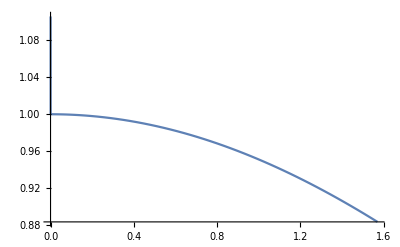

```mathematica
Plot[{(q - Sin[q])/(q^3/6)}, {q, 0, π/2}]
```